# Paso I. Variables.

```mathematica
NPart = 25; (*Número de pasos*)
init=1;end = NPart+1;
```

```mathematica
sxVar = Table[sx[i], {i, init, end}]; (*Posición en eje 0X*)

syVar = Table[sy[i], {i, init, end}]; (*Posición en eje 0Y*)
vxVar = Table[vx[i],{i, init, end}]; (*Velocidad en eje 0X*)
```

Table::iterb: Iterator {i,init,end} does not have appropriate bounds.

```mathematica
vyVar = Table[vy[i], {i, init, end}]; (*Velocidad en eje 0Y*)
```

```mathematica
ΛxVar = Table[Λx[i], {i, init, end}]; (*Aceleración artificial en el eje 0X*)
ΛyVar = Table[Λy[i], {i, init, end}]; (*Aceleración artificial en el eje 0Y*)
```

```mathematica
Vars = Join[sxVar, syVar, vxVar, vyVar, ΛxVar, ΛyVar];
```

# Paso II. Parámetros

```mathematica
(*Constante de gravitación universal*)
G=1;
(*Radio de la Tierra*)
roE=2;
(*Radio de la Luna*)
roM=1;
(*Masa de la Tierra*)
mE=10;
(*Masa de la Luna*)
mM=1;
(*Distancia entre el centro de la Tierra y el centro de la Luna*)
a = 20;
(*Vector apunta Tierra*)
rE={0,0};
(*Vector apunta Luna*)
rM={a,0};
(*Ángulo Salida*)
tethaM = Pi;
(*Ángulo Llegada*)
tethaE = 3 Pi /2;
(*Duración de la trayectoria del vuelo*)
TTT = 14*24*60*60;
TT = 1000;
T=1;
(*Partición del tiempo*)
h=T/NPart;
(*Vector direccional cohete*)
(*rR[t_]:={sx[t],sy[t]}/Sqrt[sx[t]^2+sy[t]^2];*)(*Como función*)
(*Componente apunta cohete en OX*)
rRx = Table[sxVar[[k]]/Sqrt[sxVar[[k]]^2 + syVar[[k]]^2], {k, 1, NPart+1}];
(*Componente direccional cohete en OY*)
rRy = Table[syVar[[k]]/Sqrt[sxVar[[k]]^2 + syVar[[k]]^2], {k, 1, NPart+1}];
(*Distancia Cohete-Tierra*)
dER=Table[Sqrt[sxVar[[k]]^2+syVar[[k]]^2], {k, 1, NPart+1}];
(*Distancia Cohete-Luna*)
dMR=Table[Sqrt[(sxVar[[k]]-a)^2+syVar[[k]]^2], {k, 1, NPart+1}];
(*Componentes direccionales vector Cohete-Luna*)
```

Table::iterb: Iterator {k,1,1+NPart} does not have appropriate bounds.

```mathematica
rMRx= Table[(sxVar[[k]]-rM[[1]])/Norm[{sxVar[[k]], syVar[[k]]}-rM, 2], {k, 1, NPart+1}];
rMRy= Table[(syVar[[k]]-rM[[2]])/Norm[{sxVar[[k]], syVar[[k]]}-rM, 2], {k, 1, NPart+1}];
(*Componentes direccionales vector Cohete-Tierra*)
rERx= Table[(sxVar[[k]]-rE[[1]])/Norm[{sxVar[[k]], syVar[[k]]}-rE, 2], {k, 1, NPart+1}];
rERy= Table[(sxVar[[k]]-rE[[2]])/Norm[{sxVar[[k]], syVar[[k]]}-rE, 2], {k, 1, NPart+1}];
```

# Paso III. Restricciones Igualdades. Condiciones Iniciales.

```mathematica
(*3.- Valores iniciales*)
(*Posiciones de salida del cohete*)
sInit = {sxVar[[1]]==    roE*Cos[tethaE], syVar[[1]]==    roE*Sin[tethaE]};
(*--------------------*)
(*Posiciones de llegada del cohete*)
sFinal = {sxVar[[NPart+1]]==   a+ roM*Cos[tethaM], syVar[[NPart+1]]==    roM*Sin[tethaM]};
(*--------------------*)
(*Velocidad de salida*)
v0 =50; (*m/s*)
vInit = {vxVar[[1]]==    v0*Cos[tethaE], vyVar[[1]]==    v0*Sin[tethaE]};
(*--------------------*)
(*Velocidad de llegada*)
vN = 0; (*m/s*)
vFinal = {vxVar[[NPart+1]]==    vN*Cos[tethaM], vyVar[[NPart+1]]==    vN*Sin[tethaM]}

(*----------------------------------*)
(*Aceleración de salida y llegada*)
```

{vx[26]==0,vy[26]==0}

```mathematica
RInit = Join[sInit, sFinal, vInit, vFinal]
```

{sx[1]==0,sy[1]==-2,sx[26]==19,sy[26]==0,vx[1]==0,vy[1]==-50,vx[26]==0,vy[26]==0}

# Paso IV. Restricciones Desigualdad.

```mathematica
(*Evitar la colisión con la Tierra*)
R1= Table[sxVar[[k]]^2+syVar[[k]]^2≥ roE^2 ,{k,1,NPart+1}];
(* Evitar la conlisión con la Luna*)
R2=Table[(sxVar[[k]]-a)^2+syVar[[k]]^2≥ roM^2,{k,1,NPart+1}];
(*----------------------------------*)

(*_____________________________________*)
(*Primero discretizamos el tiempo y aplicamos el Método Euler Explícito*)
Gx=-G (mM)
Fx[k_]:=Gx[[k]]+ΛxVar[[k]];
(*Parte de la expresión final*)
R3=Table[vxVar[[k+1]]==   vxVar[[k]] + .5 h (Fx[k]+Fx[k+1]),{k,1,NPart}];
Gy=Table[-((N[mM G]/dMR[[k]]^2)*rMRy[[k]]+(N[mE G]/dER[[k]]^2)*rERy[[k]]), {k, 1, NPart+1}];
Fy[k_]:=Gy[[k]]+ΛyVar[[k]];
R4=Table[vyVar[[k+1]]==   .5 (Fy[k]+Fy[k+1])*h+vyVar[[k]],{k,1,NPart}];
```

```mathematica
R5 = Table[sxVar[[k+1]]== (vxVar[[k]] + vxVar[[k+1]])*h/2+sxVar[[k]], {k, 1, NPart}];
R6 = Table[syVar[[k+1]]== (vyVar[[k]]+vyVar[[k+1]])*h*.5+syVar[[k]], {k, 1, NPart}];
R71 = Table[ΛxVar[[k]]≥ -20, {k, 1, NPart+1}];
R72 = Table[ΛxVar[[k]]≤  20, {k, 1, NPart+1}];
R81 = Table[ΛyVar[[k]]≥ -20, {k, 1, NPart+1}];
R82 = Table[ΛyVar[[k]]≤  20, {k, 1, NPart+1}];
```

```mathematica
restrictions = Join[ R3, R4,R5, R6, R71, R72, R81, R82 ,  RInit];
```

# Paso V. Función Objetivo.

```mathematica
(*5) Función Objetivo*)
(*------------------------------------------------------------------------------------*)
Objetive=Sum[Λx[tn]^2+Λy[tn]^2,{tn,1,NPart+1}];
(*Restricciones*)
Timing[SolAlt = FindMinimum[{Objetive, restrictions},Vars];]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 1.×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1899.13,0.188176,708.681}, is returned.

{211.365,Null}

```mathematica
Plots = Table[{SolAlt[[2, k, 2]], SolAlt[[2, k+NPart+1, 2]]}, {k, 1, NPart+1}]
```

{{0.,-2.},{0.097309,-3.82384},{0.400733,-5.26682},{0.9024,-6.33197},{1.56621,-7.07803},{2.36096,-7.55531},{3.2596,-7.80688},{4.23862,-7.86956},{5.27746,-7.77481},{6.35804,-7.54953},{7.46429,-7.21684},{8.5818,-6.79664},{9.69758,-6.30632},{10.7999,-5.76121},{11.8778,-5.17518},{12.9205,-4.56108},{13.9176,-3.9282},{14.8595,-3.28851},{15.7358,-2.66158},{16.5354,-2.06328},{17.2466,-1.50644},{17.8566,-1.00753},{18.3514,-0.585613},{18.7156,-0.262726},{18.9315,-0.0644989},{19.,0.}}

```mathematica
A = ListLinePlot[Plots, PlotStyle->PointSize[Large]];
```

```mathematica
B =Graphics[Circle[{0, 0}, roE]];
CC =Graphics[Circle[{a, 0}, roM]];
```

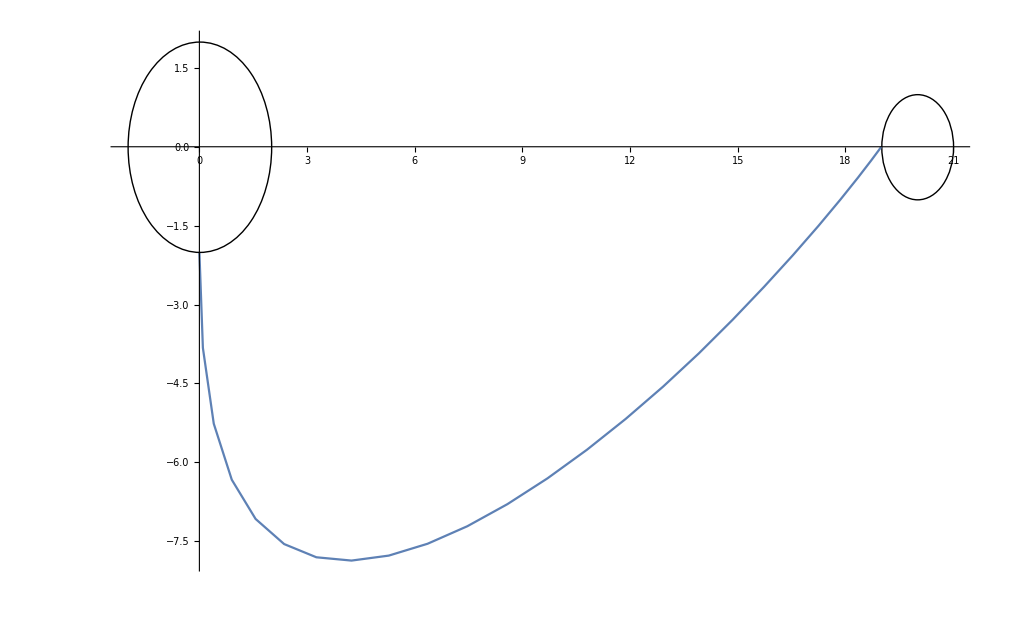

```mathematica
Show[A, B, CC, PlotRange-> All]
```